```mathematica
Clear["Global`*"];
```

```mathematica
inputSpectrum=Delete[Import["Data.xlsx", Path->NotebookDirectory[]][[1]], 1];
```

```mathematica
FirstOrder[list_]:= For[
firstOrder = List[]; i = 1; step = (list[[2,1]]-list[[1,1]]),
i ≤4,
i++,
If[i ==4,Return[firstOrder],
Which[
i == 1,firstOrder = ListConvolve[{1/step, -1/step}, list[[All, 2]]],
i == 2,firstOrder=Join[firstOrder, {(list[[-1,2]]-list[[-2,2]])/step}],
i == 3, firstOrder = Transpose[{list[[All,1]], firstOrder}]
]
]
];
SecondOrder[list_]:=For[
secondOrder = List[]; i = 1; len = Length[list]; step = (list[[2,1]]-list[[1,1]]),
i ≤ len+1,
i++, 
If[i == len+1,Return[secondOrder],
Which[
i ≤ 1,AppendTo[secondOrder, {list[[i,1]],list[[i;;i+2,2]].{-3/2, 2,-1/2}/step}],
i > 1 && i < len,AppendTo[secondOrder, {list[[i,1]],list[[i-1;;i+1,2]].{-1/2, 0,1/2}/step}],
i ≥ len,AppendTo[secondOrder, {list[[i,1]],list[[i-2;;i,2]].{1/2, -2,3/2}/step}]
]
]
];
FourthOrder[list_]:=For[
fourthOrder = List[]; i = 1; len = Length[list]; step = (list[[2,1]]-list[[1,1]]),
i ≤ len+1,
i++,
If[i == len+1,Return[fourthOrder],
Which[
i ≤ 2,AppendTo[fourthOrder, {list[[i,1]],(-25 list[[i,2]]/12 +4 list[[i+1,2]]-3list[[i+2,2]]+4 list[[i+3,2]]/3 - list[[i+4,2]] / 4)/step}],
i > 2 && i < len-1,AppendTo[fourthOrder, {list[[i,1]],(list[[i-2,2]]/12-2 list[[i-1,2]]/3+2list[[i+1,2]]/3-list[[i+2,2]]/12)/step}],
i ≥ len-1,AppendTo[fourthOrder, {list[[i,1]],-(list[[i,2]]/4 -4list[[i-1,2]]/3+3list[[i-2,2]]-4list[[i-3,2]]+25list[[i-4,2]]/12)/step}]
]
]
];
```

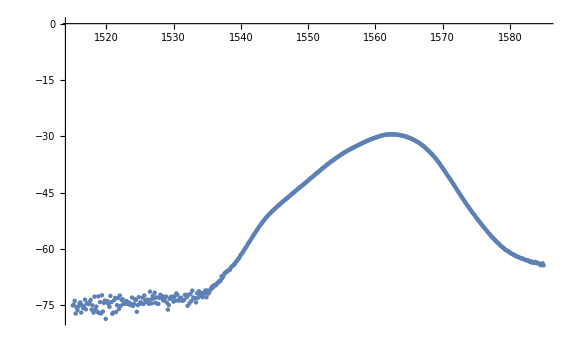

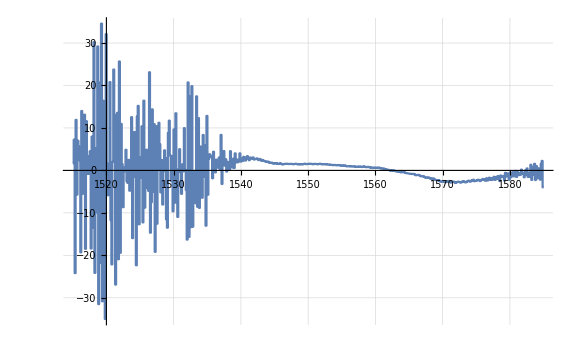

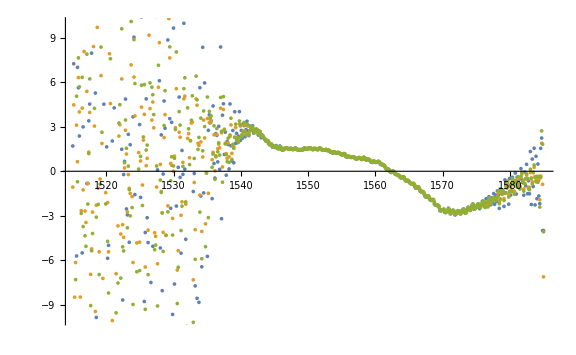

```mathematica
ListPlot[inputSpectrum, ImageSize-> Large]
Plot[Interpolation[inputSpectrum, InterpolationOrder->1]'[λ], {λ,inputSpectrum[[1,1]], inputSpectrum[[Length[inputSpectrum],1]]},
PlotRange-> Full,GridLines->Automatic,ClippingStyle-> Automatic, ImageSize->Large, MaxRecursion->10, PlotPoints->100, Exclusions->None]
ListPlot[{FirstOrder[inputSpectrum], SecondOrder[inputSpectrum], FourthOrder[inputSpectrum]}, ImageSize-> Large]
```